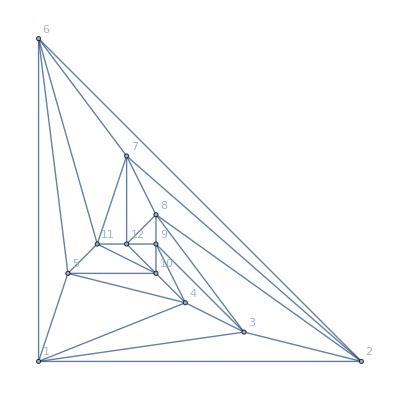

```mathematica
Graph[plantri[[1]], GraphLayout->"PlanarEmbedding", VertexLabels->"Name"]
```

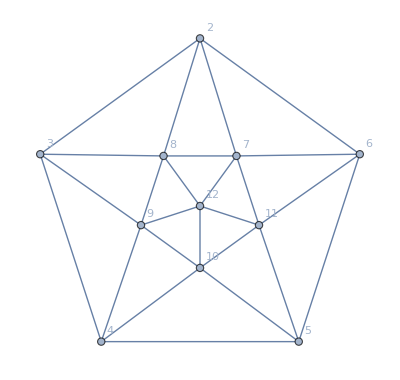

```mathematica
g= VertexDelete[Graph[plantri[[1]], GraphLayout->"TutteEmbedding", VertexLabels->"Name"],1]
```

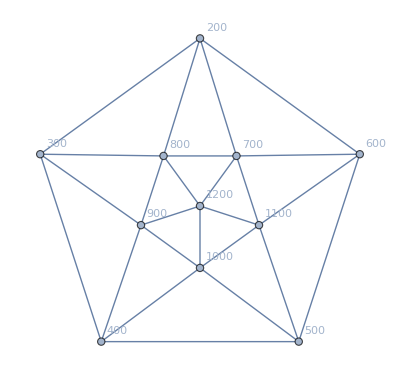

```mathematica
g2=Graph[VertexList[g]*100,Map[UndirectedEdge[#[[1]]*100,#[[2]]*100]&,EdgeList[g]], GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
```

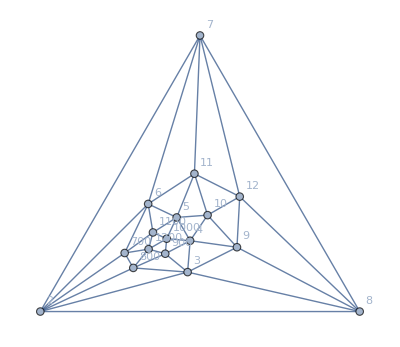

```mathematica
g3=VertexContract[VertexContract[VertexContract[VertexContract[VertexContract[GraphUnion[g,g2],{2,200}],{3,300}],{4,400}],{5,500}],{6,600},GraphLayout->"TutteEmbedding", VertexLabels->"Name"]
```

```mathematica
CollectMPGEdges[g3]
```

{7<->8,7<->11,7<->12,8<->9,8<->12,9<->10,9<->12,10<->11,10<->12,11<->12,700<->800,700<->1100,700<->1200,800<->900,800<->1200,900<->1000,900<->1200,1000<->1100,1000<->1200,1100<->1200,2<->7,2<->8,2<->700,2<->800,3<->2,3<->8,3<->9,3<->800,3<->900,4<->3,4<->9,4<->10,4<->900,4<->1000,5<->4,5<->10,5<->11,5<->1000,5<->1100,6<->2,6<->5,6<->7,6<->11,6<->700,6<->1100}

```mathematica
Length[%]
```

45

```mathematica
ChromaticPolynomial[g,x]//NullBaseCoeff
```

{0,17040,-63778,104851,-101395,64650,-28627,8953,-1955,285,-25,1}

```mathematica
ChromaticPolynomial[g3,x]//NullBaseCoeff
```

{0,69525840,-344673280,788961246,-1116652249,1101393064,-807157880,456534224,-203886157,72791543,-20863215,4785355,-868834,122327,-12900,960,-45,1}

```mathematica
Solve[2*(3N-6+1)-5==3a-6,a]
```

{{a→-3+2 N}}

```mathematica
EdgeCount[g]*2-5
```

45

```mathematica
EdgeCount[g3]
```

45

```mathematica
Table[3n-6,{n,20}]
```

{-3,0,3,6,9,12,15,18,21,24,27,30,33,36,39,42,45,48,51,54}